```mathematica
GitSetup[];
```

```mathematica
<<PkgSample`
```

```mathematica
?squareRoot
```

squareRoot[x, x0, iter] 
	Compute the square root of a number using Newton's method.
	This function will print to stdout the amount of time it took to
	execute.
		parameters:
		x: the input to the square root function.
		x0: initial guess.
		iter: number of iterations.

```mathematica
squareRoot[2, 2, 9]
```

1.41421

```mathematica
?genSwitchRandPath
```

genSwitchRandPath[
StyleBox["s", "TI"]
StyleBox[",", "TI"]
StyleBox[" ", "TI"]
StyleBox["b", "TI"]
StyleBox[",", "TI"]
StyleBox[" ", "TI"]
StyleBox["η", "TI"]
StyleBox[",", "TI"]
StyleBox[" ", "TI"]
StyleBox["dx", "TI"]
StyleBox[",", "TI"]
StyleBox[" ", "TI"]
StyleBox["dy", "TI"]
StyleBox[",", "TI"]
StyleBox[" ", "TI"]
StyleBox["num_points", "TI"]] generates a realization of the genSwitch model.

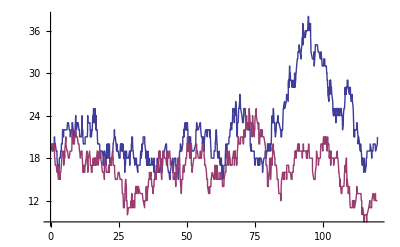

```mathematica
ListLinePlot@genSwitchRandPath[20.0, 0.1, 0.05, 0., 0., 1000]
```